# Graph Analysis on The Bus Route of Gwangju

Kyungwon Chun, kwchun@biobrain.kr
Mon. Oct. 28, 2019

```mathematica
<<SymbolicComputing`

boilerplateTemplate=StringTemplate["This notebook depends on Mathematica `ver` and MathSymbolica `scVer`. Also, the contents reflect the last execution on `date`."];
Print[boilerplateTemplate[<|"scVer"->$SCVersion,"ver"->$Version, "date"->DateString[]|>]]
```

This notebook depends on Mathematica 12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019) and MathSymbolica 5.1.2 (July 22, 2019). Also, the contents reflect the last execution on Mon 28 Oct 2019 09:43:10.

## Importing Bus Route Information of Gwangju

The following links provide the route information of the bus for Gwangju.

광주광역시의 시내버스 노선 목록 - 위키피디아

광주광역시 버스운행정보

Read the data about bus route from Wikipedia.

```mathematica
originalData=Import["https://ko.wikipedia.org/wiki/%EA%B4%91%EC%A3%BC%EA%B4%91%EC%97%AD%EC%8B%9C%EC%9D%98_%EC%8B%9C%EB%82%B4%EB%B2%84%EC%8A%A4_%EB%85%B8%EC%84%A0_%EB%AA%A9%EB%A1%9D","Data"];
```

The header of data is

```mathematica
originalData⟦1,1,2,1⟧
```

{노선,운행구간,경유지,배차 간격 (분),운행사,운행 대수,비고}

Unwrap according to the route type, and get rid of the header.

```mathematica
{none,dataExpress,dataArtery,dataBranch,dataAirport,none,none}=originalData[[1,1]];
none=.
{dataExpress,dataArtery,dataBranch,dataAirport}=Rest/@{dataExpress,dataArtery,dataBranch,dataAirport};
```

```mathematica
dataExpress={
"route"->StringTrim[#⟦1⟧,(" "|",")...],
"section"->StringTrim[{#⟦2⟧,#⟦4⟧},(" "|",")...],"stop"->StringTrim[DeleteCases[Flatten@ImportString[#⟦5⟧,"Table"],","],(" "|",")...],
"interval"->StringTrim[#⟦-4⟧,(" "|",")...],
"company"->StringTrim[#⟦-3⟧,(" "|",")...]
}&/@dataExpress;
dataArtery={
"route"->StringTrim[#⟦1⟧,(" "|",")...],
"section"->StringTrim[{#⟦2⟧,#⟦4⟧},(" "|",")...],"stop"->StringTrim[DeleteCases[Flatten@ImportString[#⟦5⟧,"Table"],","],(" "|",")...],
"interval"->StringTrim[ToString@#⟦-4⟧,(" "|",")...],
"company"->StringTrim[#⟦-3⟧,(" "|",")...]
}&/@dataArtery;
dataBranch={
"route"->StringTrim[#⟦1⟧,(" "|",")...],
"section"->StringTrim[{#⟦2⟧,#⟦4⟧},(" "|",")...],"stop"->StringTrim[DeleteCases[Flatten@ImportString[#⟦5⟧,"Table"],","],(" "|",")...],
"interval"->StringTrim[ToString@#⟦-4⟧,(" "|",")...],
"company"->StringTrim[ToString@#⟦-3⟧,(" "|",")...]
}&/@dataBranch;
dataAirport={
"route"->StringTrim[#⟦1⟧,(" "|",")...],
"section"->StringTrim[{#⟦2⟧,#⟦4⟧},(" "|",")...],"stop"->StringTrim[DeleteCases[Flatten@ImportString[#⟦5⟧,"Table"],","],(" "|",")...],
"interval"->StringTrim[ToString@#⟦-2⟧,(" "|",")...]
}&/@dataAirport;
```

Plot each route in graph.

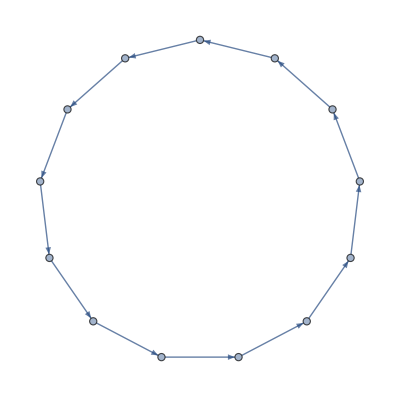
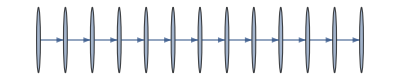
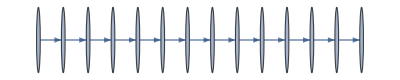
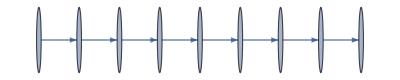
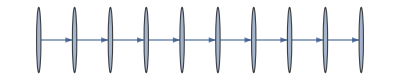
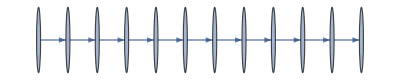

```mathematica
"stop"/.dataExpress;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
Graph/@%
```

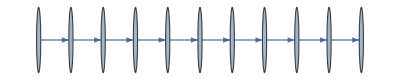
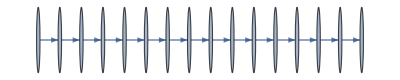
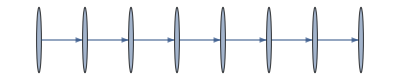
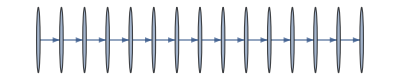
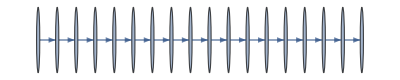
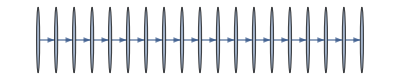
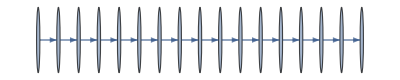
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"stop"/.dataArtery;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
Graph/@%
```

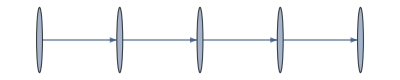
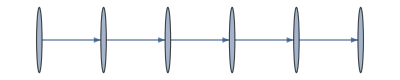
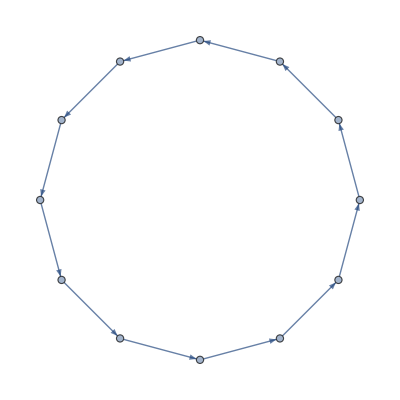
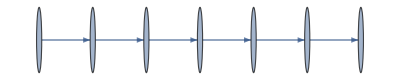
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"stop"/.dataBranch;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
Graph/@%
```

```mathematica
"stop"/.dataAirport;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
Graph/@%
```

{-Graphics-}

Represent the lists of bus stops in graphs depending on the type of route.

```mathematica
"stop"/.dataExpress;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphExpress=Graph@Flatten@%
```

-Graphics-

```mathematica
"stop"/.dataArtery;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphArtery=Graph@Flatten@%
```

-Graphics-

```mathematica
"stop"/.dataBranch;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphBranch=Graph@Flatten@%
```

-Graphics-

```mathematica
"stop"/.dataAirport;
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphAirport=Graph@Flatten@%
```

-Graphics-

Combine all types of route into one graph.

```mathematica
Flatten[EdgeList/@{graphExpress,graphArtery,graphBranch,graphAirport}];
graphAll=Graph@%
```

-Graphics-

## Graph with Tooltips

Above plots of graph are hard to identify the vertices. We can add popups to the vertices when a mouse pointer moves over it.

```mathematica
"stop"/.dataExpress;
Union@Flatten@%;
vertexLabelExpress=(#->Placed[#,Tooltip]&)/@%;
```

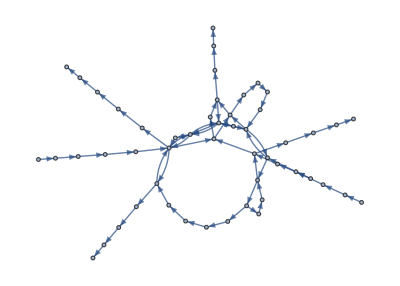

```mathematica
"stop"/.dataExpress;
(*Map[Tooltip[#,#]&,#]&/@%;*)
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphExpress=Graph[Flatten@%,VertexLabels->vertexLabelExpress]
```

```mathematica
"stop"/.dataArtery;
Union@Flatten@%;
vertexLabelArtery=(#->Placed[#,Tooltip]&)/@%;
```

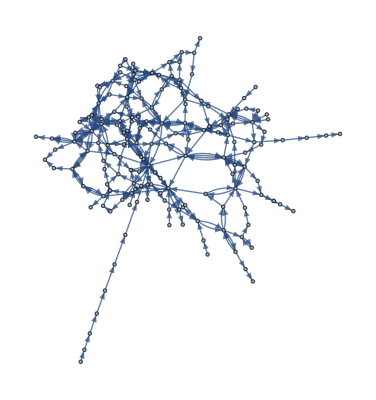

```mathematica
"stop"/.dataArtery;
(*Map[Tooltip[#,#]&,#]&/@%;*)
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphArtery=Graph[Flatten@%,VertexLabels->vertexLabelArtery]
```

```mathematica
"stop"/.dataBranch;
Union@Flatten@%;
vertexLabelBranch=(#->Placed[#,Tooltip]&)/@%;
```

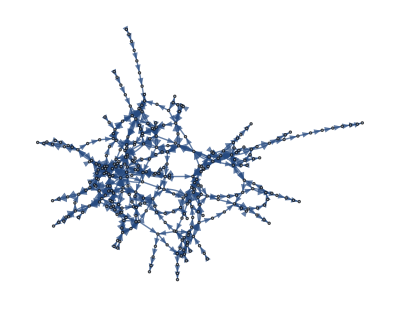

```mathematica
"stop"/.dataBranch;
(*Map[Tooltip[#,#]&,#]&/@%;*)
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphBranch=Graph[Flatten@%,VertexLabels->vertexLabelBranch]
```

```mathematica
"stop"/.dataAirport;
Union@Flatten@%;
vertexLabelAirport=(#->Placed[#,Tooltip]&)/@%;
```

```mathematica
"stop"/.dataAirport;
(*Map[Tooltip[#,#]&,#]&/@%;*)
Partition[#,2,1]&/@%;
(Rule@@@#&)/@%;
graphAirport=Graph[Flatten@%,VertexLabels->vertexLabelAirport]
```

-Graphics-

```mathematica
Flatten[VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport}];
Union@%;
vertexLabelAll=(#->Placed[#,Tooltip]&)/@%;
```

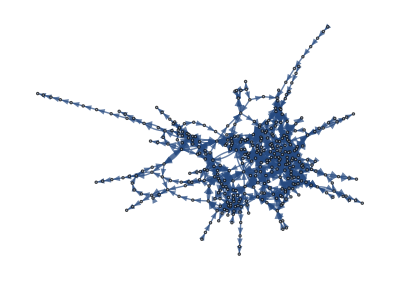

```mathematica
Flatten[EdgeList/@{graphExpress,graphArtery,graphBranch,graphAirport}];
graphAll=Graph[%,VertexLabels->vertexLabelAll]
```

## Statistics of Graphs

Number of vertices(stops) of each type of routes.

```mathematica
Length/@VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport,graphAll}
```

{52,165,333,15,379}

Some bus stops are shared among different types of routes.

```mathematica
Flatten[VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport}];
Counts@Counts@%
```

<|4→8,3→33,1→242,2→96|>

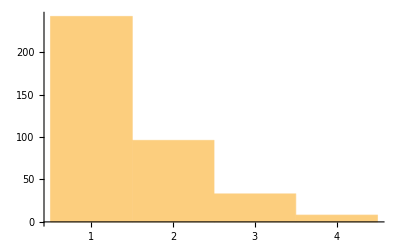

```mathematica
Flatten[VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport}];
Histogram@Counts@%
```

Number of edges of each type of routes.

```mathematica
Length/@EdgeList/@{graphExpress,graphArtery,graphBranch,graphAirport,graphAll}
```

{66,355,636,14,1071}

Statistics of graph distance between two vertices in the whole route.

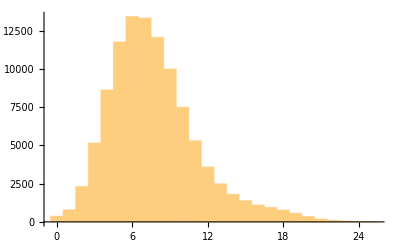

```mathematica
Histogram@Flatten@GraphDistanceMatrix@graphAll
```

## Exploratory Analysis

## The Most Umportant Stops

The number of bus stops in each route type is 565, but the number in all route graph is 379.

```mathematica
Length/@VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport,graphAll};
%//Most//Total
```

565

The following stops are common in all type of routs.

```mathematica
class4Stop=Intersection[Sequence@@(VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport})]
```

{시청,공항역,조선대,광주송정역,문화전당역,광주종합버스터미널,김대중컨벤션센터역,금남로4가역}

The subgraph of these stops is

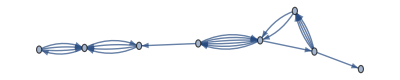

```mathematica
graphClass4Stop=Subgraph[graphAll,{"시청","공항역","조선대","광주송정역","문화전당역","광주종합버스터미널","김대중컨벤션센터역","금남로4가역"}]
```

Highlight this subgraph within each route.

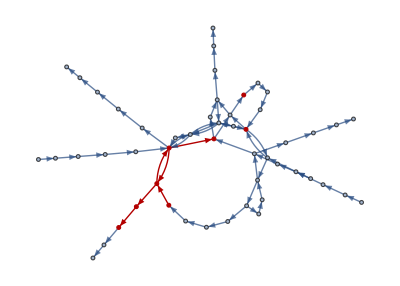
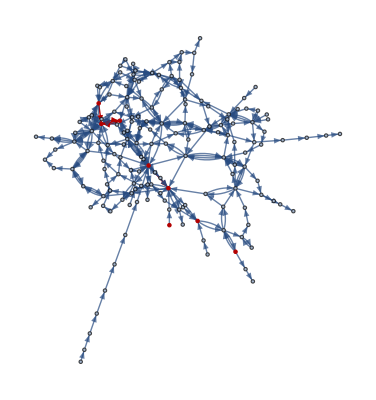
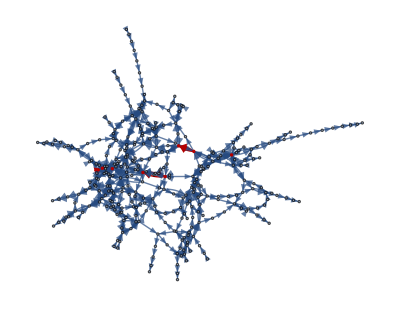
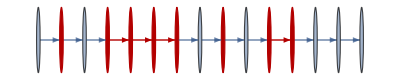
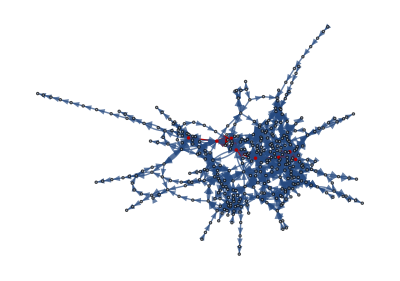

```mathematica
HighlightGraph[#,graphClass4Stop]&/@{graphExpress,graphArtery,graphBranch,graphAirport,graphAll}
```

## The Loosely Connected Stops

The following stops have only one route.

```mathematica
Flatten@(VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport});
class1Stop=Keys@Select[Counts@%,#==1&]
```

{광주역육교,빛가람혁신도시,광주김치타운입구,효천초교,우편집중국,폭스존,광주병원,신창지구,월곡2동주민센터,지실마을,장수동,월산4동,신세계백화점,하남초교,선운지구,광주무역회관,한국은행,상무병원,5.18기념공원,기아자동차,일곡사거리,쌍촌역,문화중,전남대공과대학,진곡산단,금강1길,금호저수지입구,양산호수공원,용두주공,과기원,상무시민공원,광주광역시교육청,광주교도소,화정현대아파트,동산아파트,서방사거리,.,염주체육관,상무중흥아파트,필드입구,월드컵경기장정문,비아농협,비아중흥아파트,하남공단,우산동중흥S클래스,첨단병원입구,연제현대아파트,광주박물관,풍향시장,산업인력공단,신창호반아파트,진흥고,신창동우체국,광주지방경찰청,수완세한포유,수완양우내안애,제2수원지,육판지/내지,주남,문화예술회관,산수동우체국,서남대병원,기독병원,양림휴먼시아,화정역,유동사거리,조선대병원입구,운암3동주민센터,매월동,양동시장,금남로5가역,계수초교,월곡2동행정복지센터,5.18자유공원,동천동행정복지센터,용봉현대3차아파트,유덕동주민센터,발산,요한병원,효천2지구,무진중,대촌한일베라체,서창치안센터,서창동주민센터,서광주세무서,북성중,무학초교,포충사,인성고,월산사거리,학촌,석교삼거리,대성사기러,화정중흥파크,수완우미린2차,대우디오빌,화정중,풍암동부센트레빌,대성초교,법원입구,대광여고,서창사거리,동구문화센터,빛고을복지회관,학림교,송원대학교,무등시장입구,공구단지,임정,동신대한방병원,오치한전옆,전남여고,장원초교,중앙여고,삼원맨션,용봉동성당,태령,현대자동차,연제주공아파트,박물관입구,서산초교,분토(북구),석곡동주민센터,신등,고룡정보산업학교,임곡역,연계삼거리,와산,월봉서원입구,산수보건소,본량파출소,본량초교,명도삼거리,삼도초교,동명고입구,금호타이어,동곡동주민센터,기룡마을,첨단도서관,안청농협,백길마을,신촌,윗길,전남과학대학포스트비,첨단부영아파트,유애서원,선운휴먼시아,라정시내버스,평동우체국,첨단1동행정복지센터,신가우미아파트,수완자동차매매단지,공군부대후문,송정시장,평동역,평동초교,축산시험장,복굴,송학,명화동,월곡마을,대산삼거리,우치,대봉삼거리,용성자동차학원,칠성삼거리,삼도삼거리,삼도동주민센터,마곡,도산역,신야촌,화정앞길,상촌,도산동주민센터,광주공항,럭키금속,아르네코리아,선운중학교,화순공공도서관입구,화순부영2차아파트,화순터미널,화순역,국립나무병원,농업기술원,남평농협,하칠석,대촌동주민센터,푸충사,수춘,원화리,전남학숙,노대,덕남,창평초교,고서사거리,석곡파출소,수북면사무소,강의리,서방시장,산수오거리,충장사,광주호호수생태공원,평촌,소쇄원,국립5.18국립묘지,청풍학생야영장,장성백운,남면보건지소,장성남중,남부대,국립광주과학관,진원동초교,진원면사무소,진원초교,수완새한포유,노안남초교,나주동신대,나주정렬사,본량삼거리,용호,학동(본량),보강,삼서초교,예술의거리입구,화순전남대병원입구,화장앞길,광주자동화설비공업고,하남홈플러스,정우화학,하남1교,송산유원지,신촌(본량),비엔날레전시관,동부교육청,광주고/4.19역사관,단지삼거리,영락공원,극락초교,광주시립미술관상록전시관,동구노인복지회관,두암지구입구,호남맨션}

The subgraph of these stops is

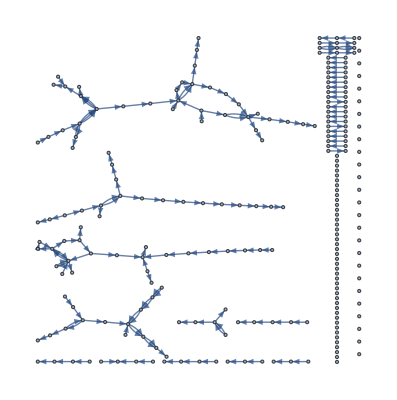

```mathematica
graphClass1Stop=Subgraph[graphAll,class1Stop]
```

Highlight this subgraph within each route.

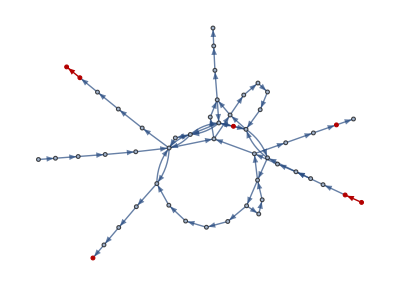
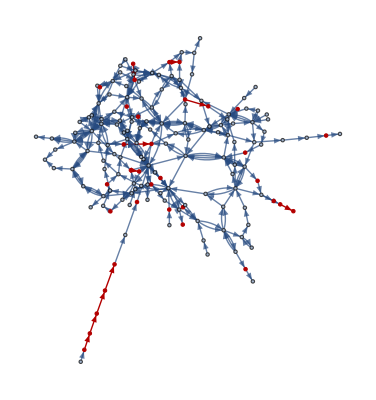
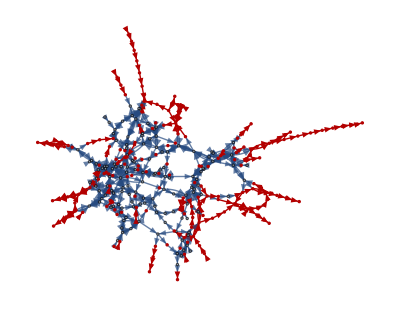
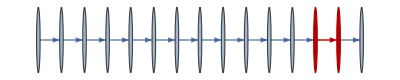
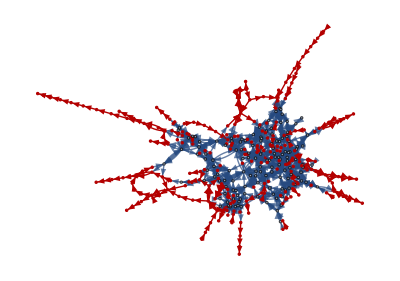

```mathematica
HighlightGraph[#,graphClass1Stop]&/@{graphExpress,graphArtery,graphBranch,graphAirport,graphAll}
```

There is a shorter path between the end stops of the airport bus route if we allow transitions.

```mathematica
FindShortestPath[graphAirport,"송정대덕아파트","지산유원지"]
GraphDistance[graphAirport,"송정대덕아파트","지산유원지"]
```

{송정대덕아파트,광주송정역,영광통,공항역,김대중컨벤션센터역,시청,광주종합버스터미널,광주일고/광주고용센터,금남로4가역,국립아시아문화전당,문화전당역,조선대,두암지구입구,호남맨션,지산유원지}

14

```mathematica
FindShortestPath[graphAll,"송정대덕아파트","지산유원지"]
GraphDistance[graphAll,"송정대덕아파트","지산유원지"]
```

{송정대덕아파트,공항역,김대중컨벤션센터역,시청,광주종합버스터미널,금남로4가역,문화전당역,전남여고,법원,지산유원지}

9

## Transition Stops between Different Types of Stops

At the following stops, we can transit to different types of routes.

```mathematica
Flatten@(VertexList/@{graphExpress,graphArtery,graphBranch,graphAirport});
transitStop=Keys@Select[Counts@%,#>1&]
```

{김대중컨벤션센터역,시청,광주종합버스터미널,경신여고,전남대사거리,조선대,남광주역,백운우체국,풍암지구,금호지구,운천저수지,상무지구입구,학동·증심사입구역,국립아시아문화전당,광주역,광천치안센터,공항역,광주송정역,동곡,광주대후문,대성여고,운남삼성아파트,수완모아엘가,응암공원,월드컵경기장,월산5동,충장치안센터,동강대,무등도서관,문흥지구입구,송하삼익아파트,백운광장,금남로4가역,동부소방서,전남대후문,북부경찰서,일곡지구,쌍암공원,첨단2동주민센터,신창중,신가주공아파트,동천마을3단지,문화전당역,전남대병원/남광주시장,조선대병원,양산지구,첨단2지구,보훈병원후문,수완지구,신가동,하남2지구,운암중,동림푸른마을,흑석사거리,경암근린공원,하남3지구모아엘가,호남대,솔뫼타운,소태역,교육대,오치한전,우치공원,용전사거리,효령노인복지타운,보훈병원,신창용수마을,운암3단지,광주-기아,챔피언스,필드,문흥지구,두암지구,법원,송원대,서영대,월곡시장,롯데백화점,양동시장역,서구청,운천역,상무역,영광통,도산동행정복지센터,앰코코리아,각화지구,국제고,첨단라인아파트,광천동,풍암사거리,전남대,유창아파트,광주공고입구,월계중,무양서원,북구청,남구청,봉선지구,대성베르힐,말바우시장,소촌금호아파트,용봉쌍용아파트,첨단2동행정복지센터,서광주전화국,동천동주민센터,동림삼익아파트,한국병원,서광주우체국,호남대광산캠퍼스,광산경찰서,정광고입구,우산시영2단지,목련마을,공구의거리,동구청,용산초교,김대중컨벤션센터,목련마을8단지,성덕마을,공군부대,송정대덕아파트,대성사거리,첨단롯데마트,광주여대,원광대한방병원,염주사거리,월산마을,전남공고,광주일고,광주고,돌고개역,문성고,송화마을,건국동주민센터,광주일고/광주고용센터,광주대입구,무등야구장,지산유원지}

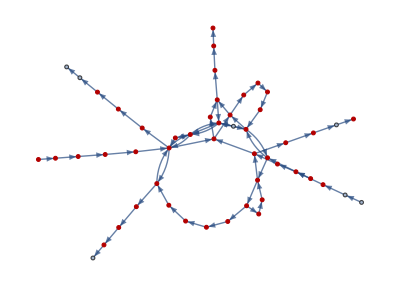
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightGraph[#,transitStop]&/@{graphExpress,graphArtery,graphBranch,graphAirport,graphAll}
```